### Binomial Probability

```mathematica
BDPr[trials_,probability_, {Optional[value_, Null],X_},Optional[times_,-1]]:=
Module[{list},
list=Table[{ n,Probability[X==n,X \[Distributed]BinomialDistribution[trials,probability]]},{n,If[times==-1,trials,times]}];
If[value =!= Null,AppendTo[list,{value,Probability[value,X\[Distributed]BinomialDistribution[trials,probability]]}]];
AppendTo[list,{"E[x]",Mean[BinomialDistribution[trials,probability]]}];
AppendTo[list,{"Var[x]",Variance[BinomialDistribution[trials,probability]]}];
AppendTo[list,{"Sd[x]",StandardDeviation[BinomialDistribution[trials,probability]]}];
list//TableForm]
```

### Normal Probability

```mathematica
PrNoramlDistPlot[mean_,sd_,{x_,Optional[x1_,Null],Optional[x2_,Null]},Optional[value_,Null]]:=Module[{Line,Area},
Line=Plot[1/(sd Sqrt[2Pi])E^(-1/2((x-mean)/sd)^2),{x,mean-sd*4,mean+sd*4},AxesLabel->{": (standard deviation)" sd,"Probability X=x"}];

If[x1=!=Null And x2 =!=Null ,{Area=Plot[1/(sd Sqrt[2Pi])E^(-1/2((x-mean)/sd)^2),{x,If[x1==-Infinity,mean-sd*4,x1],If[x2==Infinity,mean+sd*4,x2]},Filling->Axis,PlotRange->PlotRange[Line]],{Print[Show[Line,Area]],Return[Print["Pr(", x1<X<x2, ")= ",NProbability[x1<X<x2,X\[Distributed]NormalDistribution[mean,sd]]]]}},Print[Show[Line]]];
If[value=!=Null,Print["Pr(",value,")=",
NProbability[value,x\[Distributed]NormalDistribution[mean,sd]]]];
]
```

### Sampling Probability

```mathematica
SDPr[group_,success_,total_,{Optional[value_,Null],X_},Optional[times_,-1]]:=
Module[{list},
list=
Table[
{"P̂=",n,Probability[X==n,
X\[Distributed]HypergeometricDistribution[group,success,total]]},{n,If[times==-1,group,times]}];
PrependTo[list,{"P̂=",0,Probability[X==0,X\[Distributed]HypergeometricDistribution[group,success,total]]}];
If[value=!=Null,
AppendTo[list,
{"Pr",value,Probability[value,X\[Distributed]HypergeometricDistribution[group,success,total]]}]];
list//TableForm]
```

### example usage

```mathematica
BDPr[6,0.6,{X==3,X},1]
```

1 | 0.036864
X==3 | 0.27648
E[x] | 3.6
Var[x] | 1.44
Sd[x] | 1.2

PrNoramlDistPlot[150,35,{x,-∞,150}]

PrNoramlDistPlot[150,35,{x},x>150\[Conditioned]x>100]

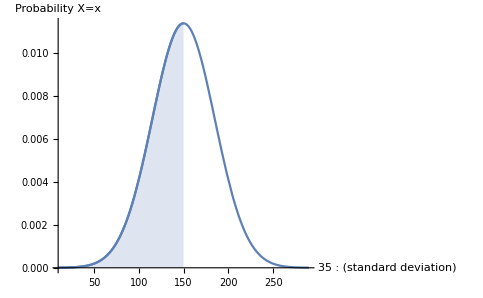

Pr(-∞<X<150)= 0.5

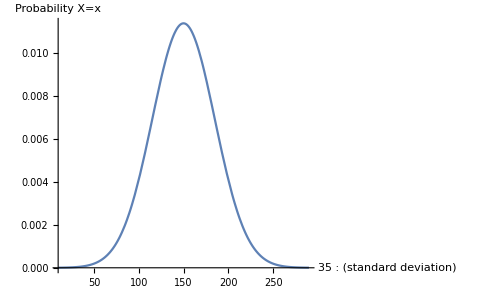

Pr(x>150\[Conditioned]x>100)=0.541456

```mathematica
PrNoramlDistPlot[150,35,{x,-Infinity,150}]
PrNoramlDistPlot[150,35,{x},x>150\[Conditioned]x>100]
```

```mathematica
SDPr[5,12,20,{x<0.7*5\[Conditioned]x>0,x}]
```

P̂= | 0 | 7/1938
P̂= | 1 | 35/646
P̂= | 2 | 77/323
P̂= | 3 | 385/969
P̂= | 4 | 165/646
P̂= | 5 | 33/646
Pr | x<3.5\[Conditioned]x>0 | 1337/1931